```mathematica
λ=.;Clear[normalgamma];(*
PDF of getting nooe electrons out for exactly λ photons in in a given pixel. Includes Gamma distribution  + Normal readout noise. Model applied to all photo electrons including darks and pCIC. sCIC neglected.

nooe = output electrons = read signal / 0.55
g = gain = 470
r = read noise = 109 electrons
λ = nb of photons you are testing for
*)normalgamma[nooe_,g_,r_,λ_]:=2^(-λ/2) ⅇ^(-nooe^2/(2 r^2)) g^-λ r^(-2+λ) ((r Hypergeometric1F1[λ/2,1/2,((-g nooe+r^2)^2)/(2 g^2 r^2)])/(√2 Gamma[(1+λ)/2])+((g nooe-r^2) Hypergeometric1F1[(1+λ)/2,3/2,((-g nooe+r^2)^2)/(2 g^2 r^2)])/(g Gamma[λ/2]))
```

Examples:

```mathematica
normalgamma[1000,500,100,2. ]
```

0.000541231

```mathematica
normalgamma[1000,500,100,2. ]
```

Poisson prior:

```mathematica
PDF[PoissonDistribution[moyvalue],λ]
```

Piecewise[{{(ⅇ^-moyvalue moyvalue^λ)/(λ!), λ≥0}, {0, True}}]

Poisson weighted distribution of λ for an observed nooe is:

```mathematica
PDF[PoissonDistribution[moyvalue],λ]normalgamma[nooe,g,r,λ]
```

Plot for moyvalue = 2:

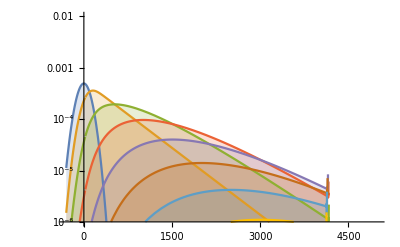

```mathematica
plot1=LogPlot[Table[PDF[PoissonDistribution[moyvalue],λ]normalgamma[noe,500,109,λ ]/.moyvalue->2,{λ,{0,1,2,3,4,5,6,7}}]//Evaluate,{noe,-300,5000},Filling->Axis,PlotRange->{{-300,5000},{.000001,.01}}]
```

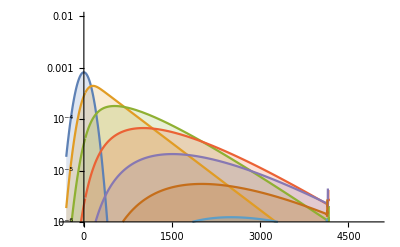

```mathematica
plot1=LogPlot[Table[PDF[PoissonDistribution[moyvalue],λ]normalgamma[noe,500,109,λ ]/.moyvalue->1.5,{λ,{0,1,2,3,4,5,6,7}}]//Evaluate,{noe,-300,5000},Filling->Axis,PlotRange->{{-300,5000},{.000001,.01}}]
```

Same without prior:

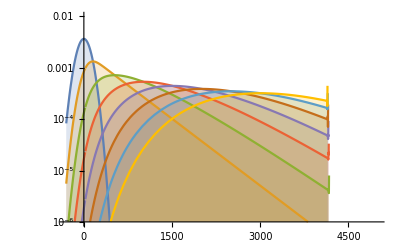

```mathematica
plot1=LogPlot[Table[normalgamma[noe,500,109,λ ],{λ,{0,1,2,3,4,5,6,7}}]//Evaluate,{noe,-300,5000},Filling->Axis,PlotRange->{{-300,5000},{.000001,.01}}]
```

Find curves intersections for threshold calculation here a bissection method, here for moylevel = 1,10,0.1  Note the upper right corner of the matrix is not useful:

```mathematica
Taballthrs=Table[

noemi0=-300;noema0=60000;
tabstart=Table[noemi=noemi0;noema=noema0;
While[noema-noemi>.1,
noech=(noemi+noema)/2;
If[
PDF[PoissonDistribution[moylevel],λ]normalgamma[noech,500,109,λ ]> PDF[PoissonDistribution[moylevel],λ+1]normalgamma[noech,500,109,λ +1],
noemi=noech,noema=noech];
];noech,{λ,0,10}];Join[{moylevel},N[tabstart]],
{moylevel,1,10,.1}
];MatrixForm[Taballthrs]
```

General::munfl: Exp[-37497.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9186.96] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(1. | 155.049 | 1023.74 | 3019.8 | 4157.28 | 4147.96 | 4138.07 | 4127.49 | 4116.45 | 4105.06 | 4093.33 | 4081.14
1.1 | 147.689 | 932.883 | 2746.64 | 4157.85 | 4148.77 | 4139.1 | 4128.87 | 4118.17 | 4107.02 | 4095.51 | 4083.67
1.2 | 140.673 | 857.09 | 2519.03 | 4158.31 | 4149.57 | 4140.02 | 4130.02 | 4119.55 | 4108.74 | 4097.47 | 4085.85
1.3 | 134.002 | 793.027 | 2326.27 | 4158.66 | 4150.15 | 4140.94 | 4131.17 | 4120.93 | 4110.24 | 4099.31 | 4087.92
1.4 | 127.676 | 738.051 | 2161.11 | 4142.21 | 4150.72 | 4141.75 | 4132.2 | 4122.08 | 4111.73 | 4100.92 | 4089.76
1.5 | 121.581 | 690.436 | 2017.8 | 4017.77 | 4151.18 | 4142.44 | 4133.01 | 4123.23 | 4113. | 4102.41 | 4091.49
1.6 | 115.83 | 648.801 | 1892.44 | 3767.38 | 4151.64 | 4143.01 | 4133.93 | 4124.27 | 4114.26 | 4103.79 | 4093.1
1.7 | 110.194 | 611.997 | 1781.68 | 3546.44 | 4152.1 | 4143.59 | 4134.62 | 4125.19 | 4115.3 | 4105.06 | 4094.59
1.8 | 104.789 | 579.333 | 1683.23 | 3350. | 4152.45 | 4144.16 | 4135.31 | 4126.11 | 4116.33 | 4106.33 | 4095.97
1.9 | 99.4981 | 550.119 | 1595.13 | 3174.14 | 4152.79 | 4144.62 | 4136. | 4126.8 | 4117.37 | 4107.48 | 4097.24
2. | 94.4375 | 523.781 | 1515.77 | 3015.89 | 4153.02 | 4145.08 | 4136.57 | 4127.6 | 4118.17 | 4108.51 | 4098.39
2.1 | 89.4919 | 499.974 | 1444. | 2872.58 | 4153.37 | 4145.54 | 4137.15 | 4128.29 | 4119.09 | 4109.43 | 4099.54
2.2 | 84.6614 | 478.351 | 1378.67 | 2742.27 | 4153.6 | 4145.89 | 4137.61 | 4128.98 | 4119.78 | 4110.35 | 4100.57
2.3 | 79.9459 | 458.569 | 1318.98 | 2623.35 | 4144.39 | 4146.23 | 4138.07 | 4129.56 | 4120.59 | 4111.27 | 4101.61
2.4 | 75.3453 | 440.397 | 1264.24 | 2514.2 | 4144.62 | 4146.58 | 4138.53 | 4130.13 | 4121.28 | 4112.08 | 4102.53
2.5 | 70.7448 | 423.72 | 1213.75 | 2413.79 | 4014.89 | 4146.81 | 4138.99 | 4130.71 | 4121.97 | 4112.88 | 4103.45
2.6 | 66.3743 | 408.308 | 1167.16 | 2321.09 | 3860.66 | 4147.15 | 4139.33 | 4131.17 | 4122.54 | 4113.57 | 4104.26
2.7 | 62.0038 | 394.047 | 1124.03 | 2235.29 | 3717.81 | 4147.38 | 4139.79 | 4131.63 | 4123.12 | 4114.26 | 4105.06
2.8 | 57.7483 | 380.705 | 1084.01 | 2155.47 | 3585.2 | 4147.61 | 4140.02 | 4132.09 | 4123.69 | 4114.95 | 4105.87
2.9 | 53.6078 | 368.284 | 1046.63 | 2081.17 | 3461.68 | 4147.84 | 4140.37 | 4132.55 | 4124.15 | 4115.53 | 4106.56
3. | 49.4674 | 356.667 | 1011.78 | 2011.82 | 3346.43 | 4148.08 | 4140.71 | 4132.89 | 4124.73 | 4116.1 | 4107.25
3.1 | 45.4419 | 345.741 | 979.118 | 1946.95 | 3238.55 | 4148.19 | 4140.94 | 4133.24 | 4125.19 | 4116.68 | 4107.94
3.2 | 41.4165 | 335.505 | 948.41 | 1886. | 3137.34 | 4148.42 | 4141.17 | 4133.58 | 4125.65 | 4117.25 | 4108.51
3.3 | 37.506 | 325.844 | 919.542 | 1828.84 | 3042.34 | 4148.54 | 4141.52 | 4133.93 | 4125.99 | 4117.71 | 4109.09
3.4 | 33.5956 | 316.758 | 892.399 | 1774.89 | 2952.86 | 4148.65 | 4141.75 | 4134.27 | 4126.45 | 4118.17 | 4109.66
3.5 | 29.8001 | 308.017 | 866.866 | 1724.17 | 2868.44 | 4148.77 | 4141.86 | 4134.5 | 4126.8 | 4118.63 | 4110.24
3.6 | 26.0047 | 299.736 | 842.598 | 1676.1 | 2788.73 | 4148.88 | 4142.09 | 4134.85 | 4127.14 | 4119.09 | 4110.81
3.7 | 22.3243 | 291.915 | 819.595 | 1630.67 | 2713.29 | 4066.07 | 4142.32 | 4135.08 | 4127.49 | 4119.55 | 4111.27
3.8 | 18.5288 | 284.439 | 797.858 | 1587.54 | 2641.75 | 3959.11 | 4142.44 | 4135.31 | 4127.83 | 4120.01 | 4111.73
3.9 | 14.9634 | 277.193 | 777.27 | 1546.71 | 2573.89 | 3857.55 | 4142.67 | 4135.54 | 4128.18 | 4120.36 | 4112.19
4. | 11.283 | 270.408 | 757.603 | 1507.83 | 2509.48 | 3761.06 | 4142.78 | 4135.77 | 4128.41 | 4120.7 | 4112.65
4.1 | 7.71761 | 263.737 | 738.856 | 1470.8 | 2448.18 | 3669.28 | 4142.9 | 4136. | 4128.75 | 4121.05 | 4113.11
4.2 | 4.1522 | 257.411 | 721.029 | 1435.61 | 2389.75 | 3581.87 | 4143.01 | 4136.23 | 4128.98 | 4121.39 | 4113.46
4.3 | 0.701809 | 251.315 | 704.007 | 1402.02 | 2333.97 | 3498.48 | 4143.13 | 4136.34 | 4129.21 | 4121.74 | 4113.92
4.4 | -2.74858 | 245.45 | 687.675 | 1369.82 | 2280.72 | 3418.89 | 4143.24 | 4136.57 | 4129.44 | 4122.08 | 4114.26
4.5 | -6.19898 | 239.699 | 672.148 | 1339.11 | 2229.89 | 3342.87 | 4143.36 | 4136.69 | 4129.67 | 4122.31 | 4114.61
4.6 | -9.64937 | 234.178 | 657.197 | 1309.78 | 2181.24 | 3270.06 | 4131.17 | 4136.92 | 4129.9 | 4122.66 | 4114.95
4.7 | -13.0998 | 228.888 | 642.82 | 1281.6 | 2134.66 | 3200.37 | 4143.59 | 4137.03 | 4130.13 | 4122.89 | 4115.3
4.8 | -16.4351 | 223.712 | 629.134 | 1254.57 | 2089.92 | 3133.54 | 4143.59 | 4137.15 | 4130.36 | 4123.12 | 4115.64
4.9 | -19.7705 | 218.767 | 615.907 | 1228.7 | 2047.02 | 3069.48 | 4143.7 | 4137.26 | 4130.48 | 4123.35 | 4115.99
5. | -23.1059 | 213.821 | 603.256 | 1203.74 | 2005.84 | 3007.95 | 4143.7 | 4137.38 | 4130.71 | 4123.58 | 4116.22
5.1 | -26.3263 | 209.106 | 591.064 | 1179.82 | 1966.28 | 2948.72 | 4143.82 | 4137.49 | 4130.82 | 4123.81 | 4116.56
5.2 | -29.6617 | 204.505 | 579.333 | 1156.81 | 1928.21 | 2891.9 | 4047.55 | 4137.61 | 4123.58 | 4124.04 | 4116.79
5.3 | -32.882 | 200.02 | 567.947 | 1134.62 | 1891.63 | 2837.16 | 3971.07 | 4137.72 | 4123.81 | 4124.27 | 4117.02
5.4 | -36.1024 | 195.649 | 557.02 | 1113.22 | 1856.32 | 2784.36 | 3897.35 | 4130.02 | 4131.28 | 4124.5 | 4117.25
5.5 | -39.3228 | 191.394 | 546.439 | 1092.64 | 1822.28 | 2733.53 | 3826.38 | 4130.13 | 4131.4 | 4124.61 | 4117.48
5.6 | -42.4281 | 187.138 | 536.318 | 1072.74 | 1789.39 | 2684.53 | 3757.95 | 4130.13 | 4131.63 | 4124.84 | 4117.71
5.7 | -45.6485 | 183.113 | 526.427 | 1053.53 | 1757.76 | 2637.26 | 3691.82 | 4130.25 | 4131.74 | 4124.96 | 4117.94
5.8 | -48.7538 | 179.087 | 516.881 | 1035.01 | 1727.16 | 2591.6 | 3627.99 | 4130.36 | 4131.86 | 4125.19 | 4118.17
5.9 | -51.9742 | 175.177 | 507.68 | 1017.07 | 1697.61 | 2547.44 | 3566.34 | 4130.36 | 4131.86 | 4125.3 | 4118.4
6. | -55.0796 | 171.381 | 498.709 | 999.706 | 1668.97 | 2504.77 | 3506.76 | 4130.48 | 4131.97 | 4125.42 | 4118.63
6.1 | -58.1849 | 167.586 | 490.083 | 982.914 | 1641.25 | 2463.36 | 3449.14 | 4130.48 | 4132.09 | 4125.65 | 4118.75
6.2 | -61.1753 | 163.905 | 481.687 | 966.582 | 1614.45 | 2423.45 | 3393.36 | 4127.37 | 4132.2 | 4125.76 | 4118.98
6.3 | -64.2806 | 160.34 | 473.521 | 950.825 | 1588.46 | 2384.69 | 3339.3 | 4126.45 | 4132.32 | 4125.88 | 4119.09
6.4 | -67.386 | 156.775 | 465.585 | 935.528 | 1563.39 | 2347.2 | 3286.86 | 4126.57 | 4132.32 | 4125.99 | 4119.32
6.5 | -70.3763 | 153.324 | 457.994 | 920.692 | 1538.89 | 2310.86 | 3236.14 | 4126.57 | 4132.43 | 4126.11 | 4119.44
6.6 | -73.3666 | 149.874 | 450.518 | 906.315 | 1515.31 | 2275.55 | 3186.91 | 4126.57 | 4132.43 | 4126.22 | 4119.67
6.7 | -76.357 | 146.538 | 443.157 | 892.399 | 1492.31 | 2241.27 | 3139.06 | 4125.88 | 4132.55 | 4126.34 | 4119.78
6.8 | -79.3473 | 143.203 | 436.141 | 878.712 | 1469.99 | 2208.03 | 3092.71 | 4125.99 | 4132.55 | 4126.45 | 4119.9
6.9 | -82.3377 | 139.868 | 429.241 | 865.6 | 1448.26 | 2175.71 | 3047.74 | 4064.12 | 4132.66 | 4126.45 | 4120.01
7. | -85.328 | 136.762 | 422.57 | 852.719 | 1427.21 | 2144.43 | 3003.92 | 4005.92 | 4132.66 | 4126.57 | 4120.13
7.1 | -88.3183 | 133.542 | 416.014 | 840.183 | 1406.74 | 2113.84 | 2961.37 | 3949.33 | 4132.66 | 4126.68 | 4120.24
7.2 | -91.3087 | 130.437 | 409.688 | 828.106 | 1386.84 | 2084.16 | 2920.08 | 3894.36 | 4132.78 | 4126.68 | 4120.36
7.3 | -94.184 | 127.331 | 403.478 | 816.26 | 1367.4 | 2055.41 | 2879.83 | 3840.76 | 4132.78 | 4126.8 | 4120.47
7.4 | -97.1744 | 124.341 | 397.382 | 804.759 | 1348.54 | 2027.23 | 2840.61 | 3788.66 | 4132.78 | 4126.91 | 4120.59
7.5 | -100.05 | 121.351 | 391.516 | 793.487 | 1330.14 | 1999.97 | 2802.54 | 3737.94 | 4132.78 | 4126.91 | 4120.7
7.6 | -102.925 | 118.36 | 385.651 | 782.561 | 1312.31 | 1973.29 | 2765.39 | 3688.6 | 4132.89 | 4127.03 | 4120.82
7.7 | -105.8 | 115.485 | 380.015 | 771.865 | 1294.83 | 1947.3 | 2729.27 | 3640.52 | 4132.89 | 4127.03 | 4120.93
7.8 | -108.791 | 112.61 | 374.494 | 761.514 | 1277.81 | 1922. | 2693.96 | 3593.6 | 4132.89 | 4127.03 | 4120.93
7.9 | -111.666 | 109.734 | 369.089 | 751.277 | 1261.25 | 1897.38 | 2659.58 | 3547.94 | 4132.89 | 4127.14 | 4121.05
8. | -114.541 | 106.974 | 363.913 | 741.386 | 1245.03 | 1873.35 | 2626.11 | 3503.43 | 4132.89 | 4127.14 | 4121.16
8.1 | -117.302 | 104.214 | 358.738 | 731.725 | 1229.27 | 1849.88 | 2593.44 | 3459.95 | 4132.89 | 4127.14 | 4121.16
8.2 | -120.177 | 101.453 | 353.677 | 722.294 | 1213.86 | 1827. | 2561.47 | 3417.51 | 4132.89 | 4127.26 | 4121.28
8.3 | -123.052 | 98.693 | 348.732 | 712.978 | 1198.79 | 1804.57 | 2530.42 | 3376.11 | 4132.89 | 4127.26 | 4121.28
8.4 | -125.928 | 96.0477 | 343.901 | 704.007 | 1184.07 | 1782.72 | 2499.94 | 3335.74 | 4132.89 | 4127.26 | 4121.39
8.5 | -128.688 | 93.4024 | 339.07 | 695.151 | 1169.7 | 1761.44 | 2470.26 | 3296.17 | 4132.78 | 4127.26 | 4121.39
8.6 | -131.563 | 90.7571 | 334.47 | 686.525 | 1155.66 | 1740.62 | 2441.28 | 3257.64 | 4132.78 | 4127.26 | 4121.51
8.7 | -134.324 | 88.2268 | 329.869 | 678.129 | 1141.86 | 1720.26 | 2412.87 | 3220.03 | 4132.78 | 4127.37 | 4121.51
8.8 | -137.084 | 85.5815 | 325.384 | 669.848 | 1128.52 | 1700.37 | 2385.15 | 3183.11 | 4132.78 | 4127.37 | 4121.62
8.9 | -139.959 | 83.0512 | 321.013 | 661.682 | 1115.29 | 1680.81 | 2358.13 | 3147.12 | 4048.13 | 4127.37 | 4121.62
9. | -142.72 | 80.5209 | 316.643 | 653.861 | 1102.53 | 1661.84 | 2331.56 | 3111.92 | 4002.93 | 4127.37 | 4121.62
9.1 | -145.48 | 77.9906 | 312.502 | 646.04 | 1089.88 | 1643.2 | 2305.68 | 3077.53 | 3958.76 | 4127.37 | 4121.62
9.2 | -148.24 | 75.5754 | 308.362 | 638.45 | 1077.57 | 1624.92 | 2280.26 | 3043.83 | 3915.52 | 4127.37 | 4121.74
9.3 | -151. | 73.1601 | 304.221 | 630.974 | 1065.49 | 1607.09 | 2255.42 | 3010.83 | 3873.19 | 4127.37 | 4121.74
9.4 | -153.761 | 70.6298 | 300.196 | 623.728 | 1053.76 | 1589.61 | 2231.15 | 2978.51 | 3831.79 | 4127.26 | 4121.74
9.5 | -156.521 | 68.2145 | 296.286 | 616.597 | 1042.15 | 1572.47 | 2207.34 | 2946.88 | 3791.3 | 4127.26 | 4121.74
9.6 | -159.281 | 65.9142 | 292.375 | 609.581 | 1030.87 | 1555.68 | 2184. | 2915.94 | 3751.51 | 4127.26 | 4121.74
9.7 | -162.042 | 63.499 | 288.58 | 602.68 | 1019.72 | 1539.23 | 2161.22 | 2885.58 | 3712.64 | 4127.26 | 4121.74
9.8 | -164.802 | 61.1987 | 284.784 | 595.895 | 1008.79 | 1523.13 | 2138.8 | 2855.9 | 3674.57 | 4127.26 | 4121.74
9.9 | -167.562 | 58.7834 | 281.104 | 589.339 | 998.211 | 1507.37 | 2116.94 | 2826.8 | 3637.19 | 4127.26 | 4121.85
10. | -170.323 | 56.4832 | 277.423 | 582.783 | 987.744 | 1491.96 | 2095.44 | 2798.28 | 3600.61 | 4127.14 | 4121.85)

Create the thresholding function (here for another threshold table having 7 as the max calculated):

```mathematica
fthrs[x_]:=Which[x<tabthrs[[1]],0,x<tabthrs[[2]],1,x<tabthrs[[3]],2,x<tabthrs[[4]],3,x<tabthrs[[5]],4,x<tabthrs[[6]],5,x<tabthrs[[7]],6,x<tabthrs[[8]],7,True,8]
```

and finally apply it to the image or table:

```mathematica
datapgnmt=Map[fthrs,datapgn/.55]
```